```mathematica
<<"C:\\Users\\Aleksey\\IdeaProjects\\MathApl\\Kernel\\MyFunction.m"
```

```mathematica
s = Import["C:\\Users\\Aleksey\\Documents\\GitHub\\stmtest\\first.txt", "List"];
```

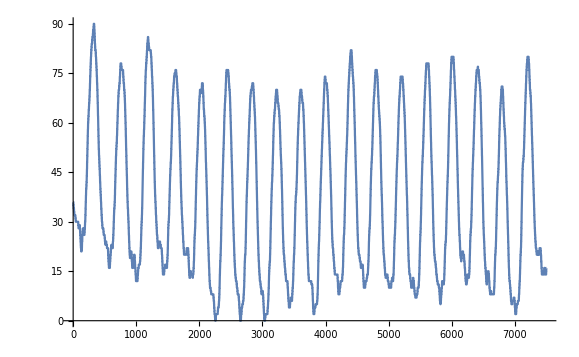

```mathematica
ListLinePlot[s]
```

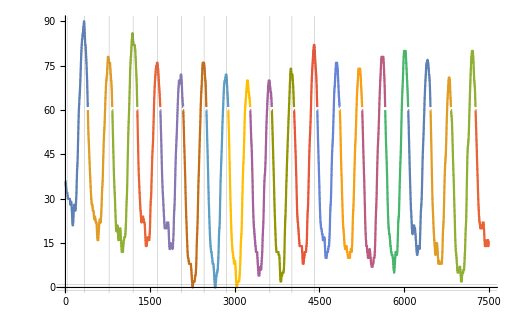

```mathematica
s;
data = Table[{i,s[[i]]},{i,Length[s]}];
splitData=Split[data, !((#1[[2]]>60.1)&& (#2[[2]]<60.1))&];
ListLinePlot[%, GridLines->{maximum, {-1,0,1}}]
```

```mathematica
e=splitData[[1]];
Max[Transpose[e][[2]]]
```

90

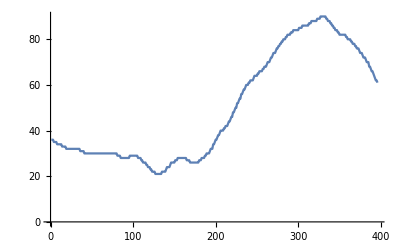

327

```mathematica
ListLinePlot[e]
Select[e,#[[2]]==Max[Transpose[e][[2]]]&][[1,1]]
```

```mathematica
Table[Select[splitData[[i]],#[[2]]==Max[Transpose[splitData[[i]]][[2]]]&][[1,1]], {i,Length[splitData]}]
```

{327,751,1185,1621,2042,2430,2840,3217,3601,3989,4400,4792,5190,5597,5997,6414,6791,7200,7265}

```mathematica
Max=31
Max=32
Max=335
Max=336
Max=774
Max=775
Max=1200
Max=1201
Max=1633
Max=1634
Max=2054
Max=2055
Max=2457
Max=2458
Max=2852
Max=2853
Max=3620
Max=4011
Max=4012
Max=4414
Max=4415
```

```mathematica
maximum = {31,335,774,1200,1630,2054,2457,2852,3620,4011,4414}
```

{31,335,774,1200,1630,2054,2457,2852,3620,4011,4414}